```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[a/y[t]Sqrt[1-y'[t]^2],y[t],t]
```

(a (-1+y'[t]^2+y[t] y''[t]))/(y[t]^2 (1-y'[t]^2)^(3/2))==0

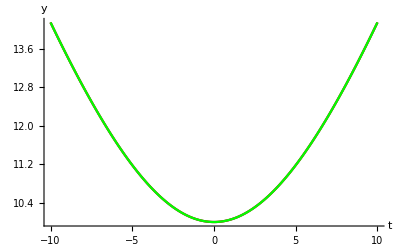

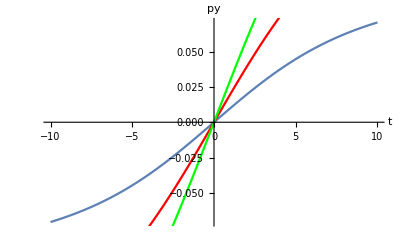

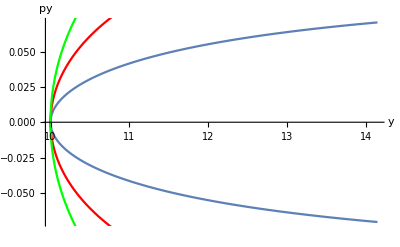

```mathematica
Block[
{y1,y2,dy,py},
y1[a1_,ys_]:=NDSolveValue[{(a (-1+y'[t]^2+y[t] y''[t]))/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1},y[0]==ys,y'[0]==0},y[t],{t,-10,10}];
y2[t1_,a_,ys_]:=y1[a,ys]/.{t->t1};
dy[t1_,a_,ys_]:=D[y1[a,ys],t]/.{t->t1};
py[t1_,a_,ys_]:=a/y2[t1,a,ys]*dy[t1,a,ys]/Sqrt[1-dy[t1,a,ys]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,2,10]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,3,10]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,2,10]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,3,10]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,10],py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,2,10],py[i,2,10]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,3,10],py[i,3,10]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Green]
]
];
]
```

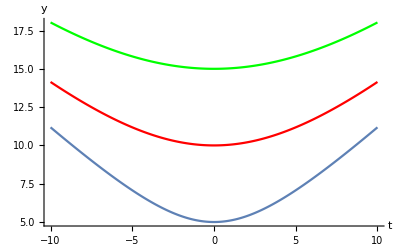

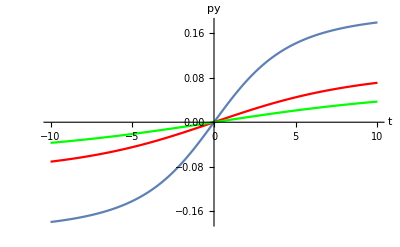

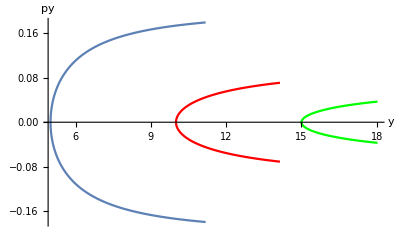

```mathematica
Block[
{y1,y2,dy,py},
y1[a1_,ys_]:=NDSolveValue[{(a (-1+y'[t]^2+y[t] y''[t]))/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1},y[0]==ys,y'[0]==0},y[t],{t,-10,10}];
y2[t1_,a_,ys_]:=y1[a,ys]/.{t->t1};
dy[t1_,a_,ys_]:=D[y1[a,ys],t]/.{t->t1};
py[t1_,a_,ys_]:=a/y2[t1,a,ys]*dy[t1,a,ys]/Sqrt[1-dy[t1,a,ys]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05]},{i,-10,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05]},{i,-10,10,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05],py[i,1,05]},{i,-10,10,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10],py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15],py[i,1,15]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```